```mathematica
Clear[data];
```

```mathematica
data=Import["Data.xlsx",Path->NotebookDirectory[]][[3]];(*спектр отражения элемента*)
spec=Import["Data.xlsx",Path->NotebookDirectory[]][[1]];(*спектр сигнала*)
data=Delete[data,1];
spec=Delete[spec,1];
```

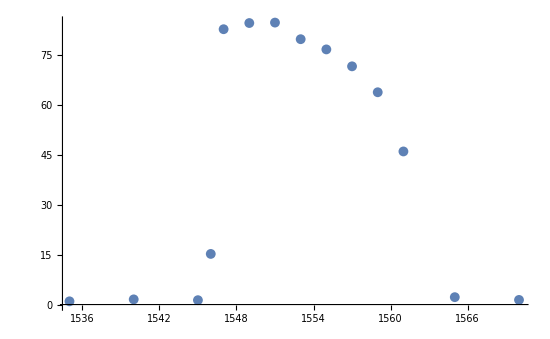

```mathematica
ListPlot[data]
```

```mathematica
intData=Interpolation[data,InterpolationOrder->1]
```

InterpolatingFunction[{{1535., 1570.}}, <>]

```mathematica
xmin=Min[data[[All,1]]];
xmax=Max[data[[All,1]]];
```

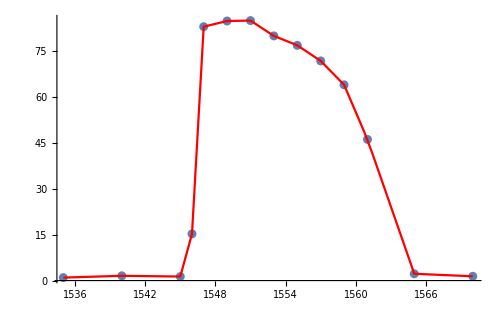

```mathematica
Show[ListPlot[data],Plot[intData[x],{x,xmin,xmax},PlotStyle->Red],PlotRange->All]
```

```mathematica
ListPlot[spec,ImageSize->Large];
```

```mathematica
spec=Select[spec,((#[[1]]≥xmin)&&(#[[1]]≤xmax))&];
```

```mathematica
(*В не логарифмическом масштабе*)
```

```mathematica
NoLogSpec=spec;
NoLogSpec[[All,2]]=10^(NoLogSpec[[All,2]]/10);
```

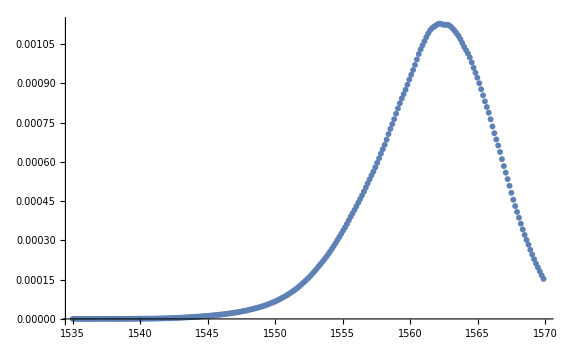

```mathematica
ListPlot[NoLogSpec,ImageSize->Large]
```

```mathematica
otrspec=spec;
```

```mathematica
otrspec[[All,2]]=NoLogSpec[[All,2]]*intData[NoLogSpec[[All,1]]]/100;
```

```mathematica
proc=Integrate[Interpolation[otrspec,InterpolationOrder->3][x],{x,xmin,xmax}]/Integrate[Interpolation[NoLogSpec,InterpolationOrder->3][x],{x,xmin,xmax}];
```

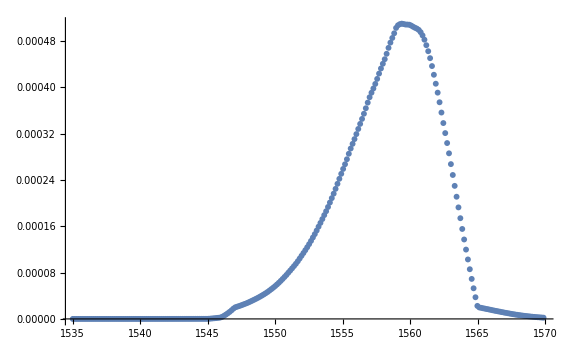

```mathematica
ListPlot[otrspec,PlotRange->All,ImageSize->Large]
```

```mathematica
(*В логарифмическом масштабе*)
```

```mathematica
LogOtrSpec=spec;
```

```mathematica
LogOtrSpec[[All,2]]=spec[[All,2]]+10*Log[intData[spec[[All,1]]]/100];
```

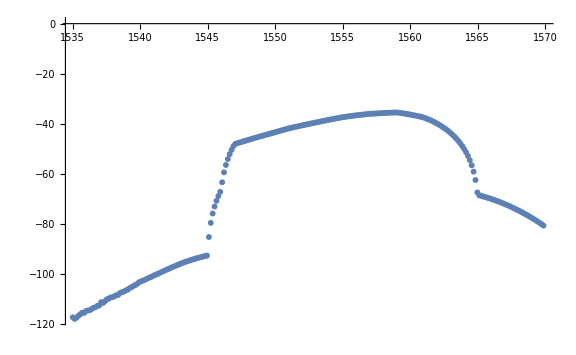

```mathematica
ListPlot[LogOtrSpec,ImageSize->Large]
```